```mathematica
nn=50;
A=SparseArray[{Band[{1,2}]->1,Band[{1,1+nn}]->1,Band[{1+nn,1}]->1,Band[{1,1}]->-4,Band[{2,1}]->1},{nn^2,nn^2}]-SparseArray[Join[Table[{nn i,nn i+1}-> 1,{i,nn-1}],Table[{nn*i+1,nn i}-> 1,{i,nn-1}]],{nn^2,nn^2}];A//MatrixForm;
```

```mathematica
ρ=-Flatten[SparseArray[{{Ceiling[nn/2],Ceiling[nn/2]}->1},{nn,nn}]];ρ//MatrixForm;
```

```mathematica
sol=Partition[LinearSolve[N[A],ρ],nn];sol//MatrixForm;
```

```mathematica
ListPlot3D[Flatten[Table[{i,j,sol[[i,j]]},{i,nn},{j,nn}],1],PlotRange->All]
```

-Graphics3D-

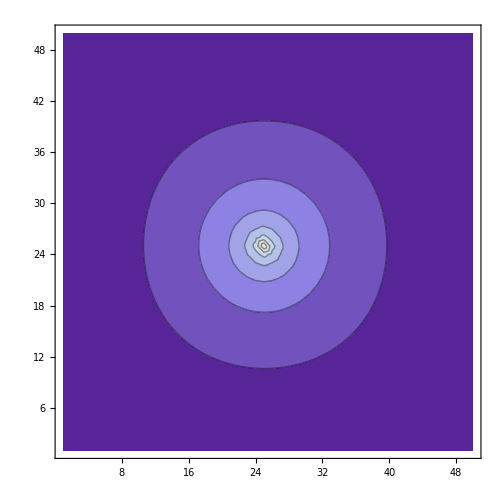

```mathematica
ListContourPlot[Flatten[Table[{i,j,sol⟦i,j⟧},{i,nn},{j,nn}],1],PlotRange->All]
```